Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 10

Metoda odchyłek ważonych

Napisać procedurę realizującą metodę odchyłek ważonych dla równania:

u''(x)-u'(x)=0,   x∈(0,1),

z warunkami brzegowymi:

u(0)=1,
u'(1)=2.

Funkcje kształtu nie muszą zapewniać spełnienia warunków brzegowych.

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone przyjmując jako funkcje kształtu:

Φ_1(x)=1,   
Φ_2(x)=x,   
Φ_3(x)=x^2,  

a jako funkcje wagowe:

w_1(x)=1,   
w_2(x)=x,   
w_3(x)=x^2.

Jako funkcje wagowe na brzegu przyjąć funkcje w_i.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

b) Wykonać te same obliczenia dla funkcji kształtu postaci:

Φ_1(x)=1,   
Φ_2(x)=exp x .   

Jako funkcje wagowe przyjąć pierwsze dwie funkcje wagowe z poprzedniego zadania.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym.

## Rozwiązanie

### Kod procedury

Procedura realizuje metodę odchyłek ważonych przy założeniu, że funkcje kształtu spełniają zadane warunki brzegowe.

Rozważane jest równanie:
	A(T(x)) = B(x) dla x∈(a,b) oraz T(x) = φ(x) dla x∈{a,b}.
Wejście:
	operatorA - operator różniczkowy A;
	BB - funkcja B;
	Ω - przedział (a,b);
	φ - funkcja zadana na brzegu;
	q - funkcja zadana na brzegu;
	Γ1 - brzeg;
	wagi, - układ liniowo niezależnych funkcji wagowych;
	wagib1 - jak wyżej;
	wagib2 - j. w.;
	bazowe - funkcje kształtu;
	z - zmienna.
Wyjście:
	rozwiązanie przybliżone lub dokładne.

```mathematica
Clear[mow];
mow[operatorA_,BB_,Ω_,φ_,q_,Γ1_,wagi_,wagib1_,wagib2_,bazowe_,z_Symbol]:=Module[{AA=operatorA,R0,R1,R2,w=wagi,wb1=wagib1,wb2=wagib2,n=Length[bazowe],T,uklad,rozwiazanie},

T[x_]:=Sum[p[i]*Function[bazowe[[i]]][x],{i,1,n}];
(*R0[x_]:=AA[x][T[x]]-BB[x];*)
R0[x_]=(AA[x][#]-BB[x])&;
(*R1[x_]:=T[x]-φ[x];*)
R1[x_]=(#-φ[x])&;
(*R2[x_]:=T'[x]-q[x];*)
R2[x_]=(D[#,x]-q[x])&;

(*uklad=Table[∫_Ω⟦1⟧^Ω⟦2⟧ (w⟦i⟧&)[x] R0[x][T[x]]ⅆx+∫_Γ1⟦1⟧^Γ1⟦2⟧ (wb1⟦i⟧&)[x] R1[x][T[x]]ⅆx+∫_Γ2⟦1⟧^Γ2⟦2⟧ (wb2⟦i⟧&)[x] R2[x][T[x]]ⅆx==0,{i,n}];*)
uklad=Table[∫_Ω⟦1⟧^Ω⟦2⟧ (w⟦i⟧&)[x] R0[x][T[x]]ⅆx+(((wb1⟦i⟧&)[x] R1[x][T[x]])/.{x->Ω[[1]]})+(((wb2⟦i⟧&)[x] R2[x][T[x]])/.{x->Ω[[2]]})==0==0,{i,n}];
(*uklad=Table[∫_Ω⟦1⟧^Ω⟦2⟧ (w⟦i⟧&)[x] R0[x][T[x]]ⅆx+(wb1⟦i⟧&)[x] R1[x][T[Ω[[1]]]]+(wb2⟦i⟧&)[x] R2[x][T[Ω[[2]]]]==0==0,{i,n}];*)

rozwiazanie=Solve[uklad,Table[p[i],{i,n}]];
(*Print["rozwiazanie ",rozwiazanie];*)

Return[Sum[rozwiazanie[[1,i,2]]*Function[bazowe[[i]]][z],{i,1,n}]]
]
```

### Norma w L^p

```mathematica
normaLp[f_,p_,a_,b_]:=Module[{norma},
norma=(∫_a^b Abs[f[x]]^p ⅆx)^(1/p);
Return[norma]]
```

### Przykład 1.2 z wykładu

```mathematica
Clear[p,op,BB,Ω,φ,q,Γ1,wagi,wagib1,wagib2,bazowe,z];
op[t_]=(D[#,{t,2}]-D[#,t])&;
BB[x_]:=0;
Ω={0,1};
φ[x_]:=Piecewise[{{1,x==0}}];
q[x_]:=Piecewise[{{2,x==1}}]
Γ1={0,1};
bazowe={1,Exp[x]};
wagi={1,x};
wagib1=wagi;
wagib2=wagi;
mow[op,BB,Ω,φ,q,Γ1,wagi,wagib1,wagib2,bazowe,z]
```

-(2-ⅇ)/ⅇ+2 ⅇ^(-1+x)

### ad a)

```mathematica
Clear[p,op,BB,Ω,φ,q,Γ1,wagi,wagib1,wagib2,bazowe,z];
op[t_]=(D[#,{t,2}]-D[#,t])&;
BB[x_]:=0;
Ω={0,1};
φ[x_]:=Piecewise[{{1,x==0}}];
q[x_]:=Piecewise[{{2,x==1}}]
Γ1={0,1};
bazowe={1,x,x^2};
wagi=bazowe;
wagib1=wagi;
wagib2=wagi;
przyblizone=mow[op,BB,Ω,φ,q,Γ1,wagi,wagib1,wagib2,bazowe,z]
```

15/17+(12 x)/17+(12 x^2)/17

```mathematica
dokladne=DSolve[{op[x][u[x]]==BB[x],u[Ω[[1]]]==φ[Ω[[1]]],u'[Ω[[2]]]==q[Ω[[2]]]},u[x],x][[1,1,2]]
```

(-2+ⅇ+2 ⅇ^x)/ⅇ

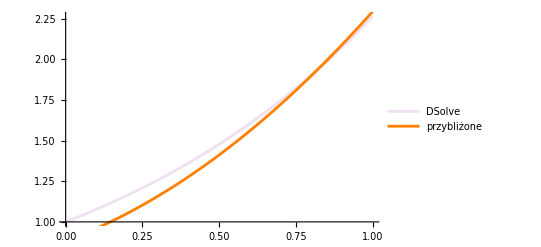

```mathematica
Show[Plot[dokladne,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"DSolve"},PlotStyle->LightPurple],Plot[przyblizone,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"przybliżone"},PlotStyle->Orange]]
```

```mathematica
Clear[f];
f[x_]:=przyblizone-dokladne;
normaLp[f,2,Ω[[1]],Ω[[2]]]
```

(√(2/5 (7225-2720 ⅇ+27 ⅇ^2)))/(17 ⅇ)

```mathematica
%//N
```

0.0759288

### ad b)

```mathematica
Clear[p,op,BB,Ω,φ,q,Γ1,wagi,wagib1,wagib2,bazowe,z];
op[t_]=(D[#,{t,2}]-D[#,t])&;
BB[x_]:=0;
Ω={0,1};
φ[x_]:=Piecewise[{{1,x==0}}];
q[x_]:=Piecewise[{{2,x==1}}]
Γ1={0,1};
bazowe={1,Exp[x]};
wagi={1,x};
wagib1=wagi;
wagib2=wagi;
przyblizone=mow[op,BB,Ω,φ,q,Γ1,wagi,wagib1,wagib2,bazowe,z]
```

-(2-ⅇ)/ⅇ+2 ⅇ^(-1+x)

```mathematica
dokladne=DSolve[{op[x][u[x]]==BB[x],u[Ω[[1]]]==φ[Ω[[1]]],u'[Ω[[2]]]==q[Ω[[2]]]},u[x],x][[1,1,2]]
```

(-2+ⅇ+2 ⅇ^x)/ⅇ

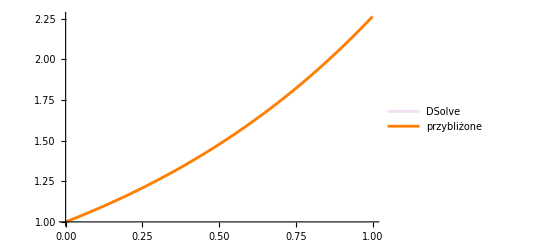

```mathematica
Show[Plot[dokladne,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"DSolve"},PlotStyle->LightPurple],Plot[przyblizone,{x,Ω[[1]],Ω[[2]]},PlotLegends->{"przybliżone"},PlotStyle->Orange]]
```

```mathematica
Clear[f];
f[x_]:=przyblizone-dokladne;
normaLp[f,2,Ω[[1]],Ω[[2]]]
```

0

```mathematica
%//N
```

0.